# MS-C2105: Introduction to Optimization // Week 1

Harri Hakula, 2022

## First Optimisation Model

Our first optimisation problem

```mathematica
max z==800 Subscript[x, 1]+600 Subscript[x, 2]
3 Subscript[x, 1]+5 Subscript[x, 2]≤40
7 Subscript[x, 1]+4 Subscript[x, 2]≤60
Subscript[x, 1],Subscript[x, 2]≥0
```

## Feasible Region: First Constraint

Inequality on the plane

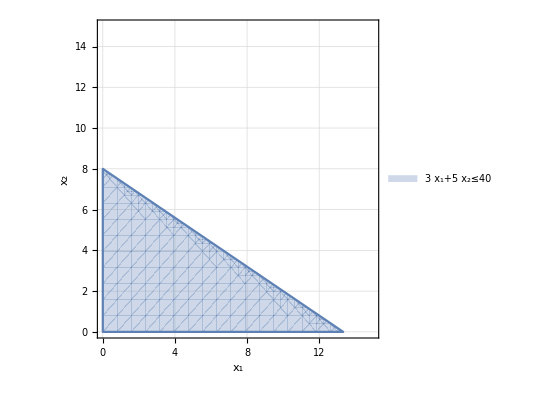

```mathematica
RegionPlot[3 Subscript[x, 1]+5 Subscript[x, 2]≤40,{Subscript[x, 1],0,15},{Subscript[x, 2],0,15},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{3 Subscript[x, 1]+5 Subscript[x, 2]≤40}]
```

## Feasible Region: Adding Second Constraint

Inequality on the plane: Effect of multiple constraints

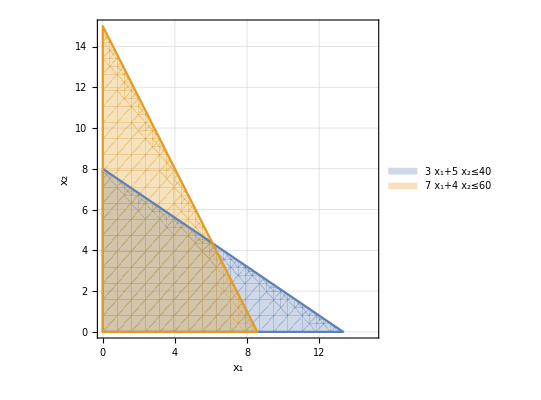

```mathematica
RegionPlot[{3 Subscript[x, 1]+5 Subscript[x, 2]≤40,7 Subscript[x, 1]+4 Subscript[x, 2]≤60},{Subscript[x, 1],0,15},{Subscript[x, 2],0,15},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic,PlotLegends->{3 Subscript[x, 1]+5 Subscript[x, 2]≤40,7 Subscript[x, 1]+4 Subscript[x, 2]≤60}]
```

## Feasible Region

Feasible region emerges, remember that the objective function does not play any role yet!

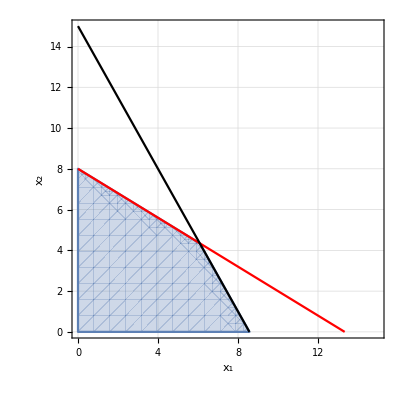
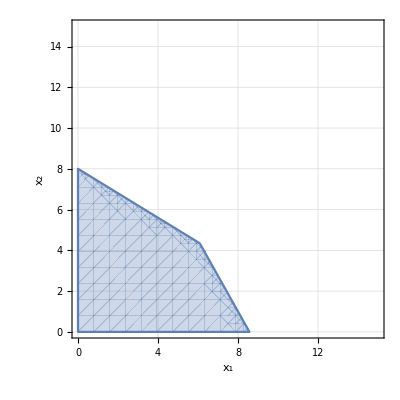

```mathematica
base=RegionPlot[{3 Subscript[x, 1]+5 Subscript[x, 2]≤40&&7 Subscript[x, 1]+4 Subscript[x, 2]≤60},{Subscript[x, 1],0,15},{Subscript[x, 2],0,15},FrameStyle->Directive[Thick,16],FrameLabel->Automatic,GridLines->Automatic];
base2=Show[base,ContourPlot[{3 Subscript[x, 1]+5 Subscript[x, 2]==40,7 Subscript[x, 1]+4 Subscript[x, 2]==60},{Subscript[x, 1],0,15},{Subscript[x, 2],0,15},FrameStyle->Directive[Thick,16],FrameLabel->{Subscript[x, 1],Subscript[x, 2]},GridLines->Automatic,ContourStyle->{Red,Black}]];
Row[{base2,base}]
```

## Feasible Region: Adding Objective Function

The objective function has its fixed slope, but the intercept is not fixed.

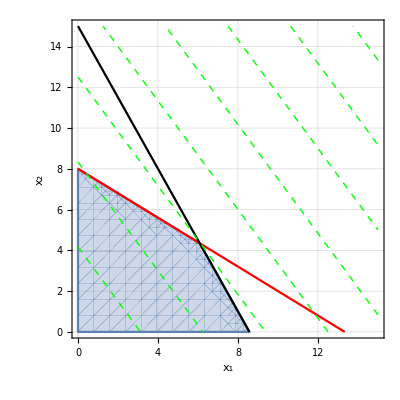

```mathematica
Show[base2,ContourPlot[{800 Subscript[x, 1]+600 Subscript[x, 2]},{Subscript[x, 1],0,15},{Subscript[x, 2],0,15},ContourShading->None,ContourStyle->{{Thick,Green,Dashed}},FrameStyle->Directive[Thick,16],FrameLabel->{Subscript[x, 1],Subscript[x, 2]},GridLines->Automatic]]
```

## Feasible Region: 3D

It is easier to see what is going on if we let the objective function be the plane it is. (Or is it?) The intercepts above represent contours on the plane!

```mathematica
full=Plot3D[{800 Subscript[x, 1]+600 Subscript[x, 2]},{Subscript[x, 1],0,9},{Subscript[x, 2],0,9},MeshFunctions->{#3&},Mesh->10,BoundaryStyle->Directive[Red,Thick],BoxRatios->1,RegionFunction->Function[{x,y},3x+5y≤40&&7x+4y≤60&&x≥0&&y≥0],AxesLabel->Automatic,AxesStyle->Directive[Thick,16],ImageSize->Large]
```

-Graphics3D-

## Feasible Region: Constraints

The constraints have not really disappeared, they are planes themselves.

```mathematica
Show[full,
ContourPlot3D[{7x+4y==60,3x+5y==40},{x,0,9},{y,0,9},{z,0,8000},AxesStyle->Directive[Thick,16]],ImageSize->Large
]
```

-Graphics3D-